```mathematica
Clear[x]
```

```mathematica
funk[x_]:=0.2*PDF[NormalDistribution[1,0.25],x]+0.6*PDF[NormalDistribution[4,1.25],x]+0.2*PDF[NormalDistribution[7,0.25],x]
```

```mathematica
funk[y] (*put in your distribution evaluation here*)
```

```mathematica
Integrate[funk[a],{a,-100,100}] (* check to see if it is a valid probability distribution *)
```

```mathematica
1
```

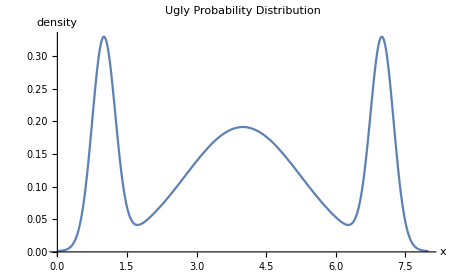

```mathematica
Plot[funk[x],{x,0,8},PlotLabel->"Ugly Probability Distribution",AxesLabel->{"x","density"}]
```

```mathematica
RandStep[x_]:=RandomVariate[NormalDistribution[x,stepsigma]](*this is our random step function, which draws from normal distribution. remember to set the step size*)
```

```mathematica
stepsigma=1; (*this is actually a really tricky parameter to set; might need to play around with it *)
x=2;
STEPS=100000; (*this is the total number of steps our MCMC will take before the burn in*)
sample={x}; (*setting up a list to store vectors*)
For[i=1,i≤STEPS,i++,
U=RandomVariate[UniformDistribution[{0,1}]]; (* generates U~U(0,1) *)
propstep=RandStep[x];  (*proposes a random step to a point on funky*)
rejectcrit=Min[funk[propstep]/funk[x],1]; (*sets rejection criterion*)
If[U<rejectcrit,x=propstep,x=x]; (*either accepts or rejects proposed step*)
sample=Append[sample,x]; (*adds a number to the sampling list*)
] (*sampling list should converge to desired distribution*)
```

General::munfl: 0.2 4.996169580074×10^-317 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.2 5.397914570241×10^-357 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.2 3.123534978752×10^-322 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
burnedin=Table[sample[[i]],{i,25,STEPS}]; (* eliminate some of the first iterations while the algorithm finds the distribution*)
```

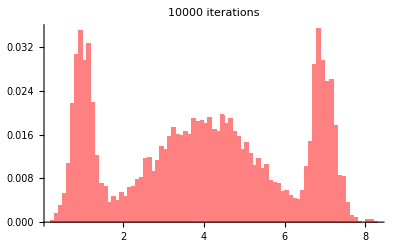

```mathematica
bins=100;
milk=Plot[1/10*funk[x],{x,0,8}];
choclate=Histogram[burnedin,bins,"Probability",ChartStyle->Pink,PlotLabel->"Approximation of the Disrtribution"] (* approximates  *)
```

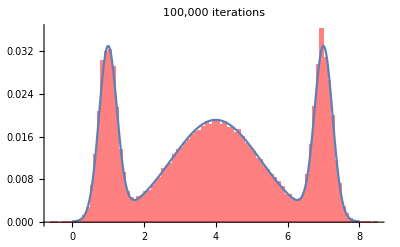

```mathematica
Show[choclate,milk]
```